## The RGB Cube corners.

```mathematica
RGBCube = {{0,1,1,0,0,0,1,1},{0,0,1,1,1,0,0,1},{0,0,0,0,1,1,1,1}};
faces = {{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}}
MatrixForm[RGBCube]
```

{{1,2,3,4},{5,6,7,8},{1,2,7,6},{2,3,8,7},{3,4,5,8},{1,4,5,6}}

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

## Rotation Matrices

```mathematica
RotationMatrixX[α_]:={{1, 0, 0}, {0, Cos[α], Sin[α]}, {0, -Sin[α], Cos[α]}};
RotationMatrixY[β_]:={{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}};
RotationMatrixZ[γ_]:={{Cos[γ], Sin[γ], 0}, {-Sin[γ], Cos[γ], 0}, {0, 0, 1}};
R[α_,β_, γ_]:=RotationMatrixZ[γ].RotationMatrixY[β].RotationMatrixX[α]
```

Solution for the Yab cube. Luminocity axis is in the X value.

```mathematica
YAB[θ_]:=RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
Print[MatrixForm[FullSimplify[YAB[θ]]].MatrixForm[RGBCube],"=",MatrixForm[FullSimplify[YAB[θ]. RGBCube]]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | -Cos[θ]/(√6)+Sin[θ]/(√2)
-Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6)).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -Cos[θ]/(√6)-Sin[θ]/(√2) | Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | Cos[θ]/(√6)+Sin[θ]/(√2) | -Cos[θ]/(√6)+Sin[θ]/(√2) | -√(2/3) Cos[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

```mathematica
YABCube[θ_]:=FullSimplify[YAB[θ].RGBCube]
```

```mathematica
MatrixForm[YABCube[θ]]
```

(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -Cos[θ]/(√6)-Sin[θ]/(√2) | Cos[θ]/(√6)-Sin[θ]/(√2) | √(2/3) Cos[θ] | Cos[θ]/(√6)+Sin[θ]/(√2) | -Cos[θ]/(√6)+Sin[θ]/(√2) | -√(2/3) Cos[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)-Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)+Sin[θ]/(√6) | √(2/3) Sin[θ] | 0)

```mathematica
Manipulate[corners = Transpose[YABCube[θ]];Graphics3D[{Polygon[corners[[faces[[1]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[1]]]]]]],Polygon[corners[[faces[[2]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[2]]]]]]],Polygon[corners[[faces[[3]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[3]]]]]]],Polygon[corners[[faces[[4]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[4]]]]]]],Polygon[corners[[faces[[5]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[5]]]]]]],Polygon[corners[[faces[[6]]]],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[faces[[6]]]]]]]},Lighting->"Neutral"],{θ,0,Pi}]
```

```mathematica
MatrixForm[{TrigExpand[YABCube[θ +Pi/6][[2]]],YABCube[θ ][[3]]}]
```

(0 | -Cos[θ]/(√2)-Sin[θ]/(√6) | Cos[θ]/(√2)-Sin[θ]/(√6) | √(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6) | -Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | 0
0 | -Cos[θ]/(√2)+Sin[θ]/(√6) | -√(2/3) Sin[θ] | Cos[θ]/(√2)+Sin[θ]/(√6) | Cos[θ]/(√2)-Sin[θ]/(√6) | √(2/3) Sin[θ] | -Cos[θ]/(√2)-Sin[θ]/(√6) | 0)

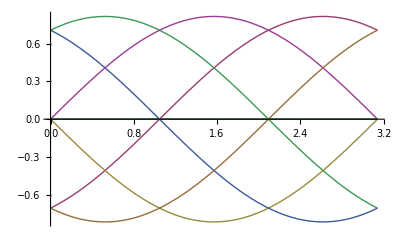

```mathematica
Plot[Evaluate[YABCube[θ][[3]], {θ, 0, Pi}]]
```

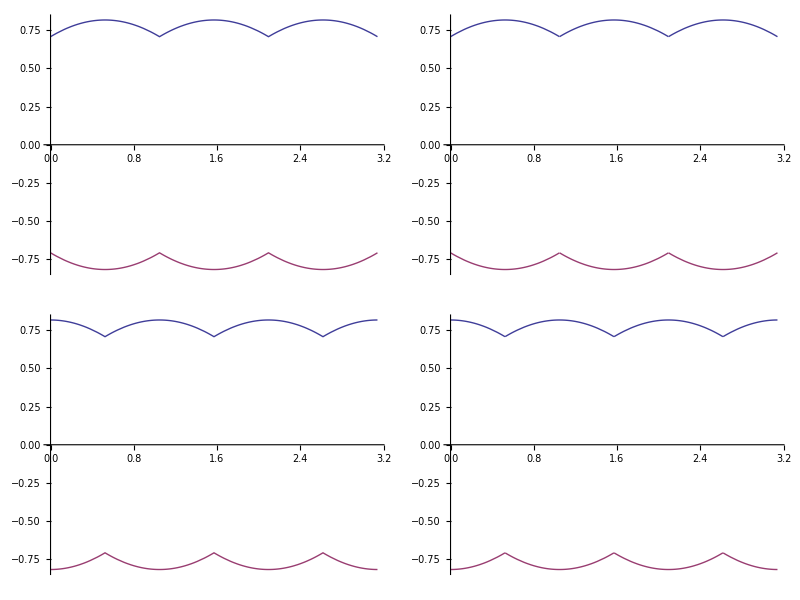

```mathematica
Grid[{{Plot[{Max[YABCube[θ ][[3]]],Min[YABCube[θ ][[3]]]},{θ,0,Pi}], Plot[{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)},{θ,0,Pi}]},{Plot[{Max[YABCube[θ ][[2]]],Min[YABCube[θ ][[2]]]},{θ,0,Pi}],Plot[{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{θ,0,Pi}]}}]
```

```mathematica
YABPolygon[θ_]:=Transpose[{Take[YABCube[θ ][[2]],{2,7}],Take[YABCube[θ ][[3]],{2,7}]}]
```

```mathematica
Manipulate[Graphics[{Black,Rectangle[Sequence@@Transpose[{YABAxisRanges[θ ][[2]],YABAxisRanges[θ ][[3]]}]],Blue,Polygon[YABPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube][[{2,3,4,5,6,7}]]]]]},PlotRange->{{-√(2/3) ,√(2/3) },{-√(2/3) ,√(2/3) }}],{θ,0,Pi}]
```

Take::take: Cannot take positions 2 through 7 in {{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}}.

Part::partw: Part 3 of scaleMatrix . {{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}} does not exist.

Take::take: Cannot take positions 2 through 7 in (scaleMatrix . {{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}}) ⟦ 3 ⟧.

Transpose::nmtx: The first two levels of the one-dimensional list {Take[{{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}}, {2, 7}], Take[« 1 », {2, 7}]} cannot be transposed.

Take::take: Cannot take positions 2 through 7 in {{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}}.

Part::partw: Part 3 of scaleMatrix . {{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}} does not exist.

Take::take: Cannot take positions 2 through 7 in (scaleMatrix . {{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}}) ⟦ 3 ⟧.

Transpose::nmtx: The first two levels of the one-dimensional list {Take[{{0., 0.57735, 1.1547, 0.57735, 1.1547, 0.57735, 1.1547, 1.73205}, {0., -0.607918, -0.776004, -0.168086, 0.607918, 0.776004, 0.168086, 1.11022×10^-16}, {0., 0.545071, -0.253937, -0.799008, -0.545071, 0.253937, 0.799008, 0.}}, {2, 7}], Take[« 1 », {2, 7}]} cannot be transposed.

```mathematica
YABAxisRanges[θ_]:={{0,Sqrt[3]},{Cos[Mod[θ -Pi/6,Pi/3]]/(√2)+Sin[Mod[θ-Pi/6,Pi/3]]/(√6),(-Cos[Mod[θ-Pi/6,Pi/3]])/(√2)-Sin[Mod[θ-Pi/6,Pi/3]]/(√6)},{Cos[Mod[θ,Pi/3]]/(√2)+Sin[Mod[θ,Pi/3]]/(√6),(-Cos[Mod[θ,Pi/3]])/(√2)-Sin[Mod[θ,Pi/3]]/(√6)}};
YABAxisRanges[θ]
```

{{0,√3},{Cos[Mod[-π/6+θ,π/3]]/(√2)+Sin[Mod[-π/6+θ,π/3]]/(√6),-Cos[Mod[-π/6+θ,π/3]]/(√2)-Sin[Mod[-π/6+θ,π/3]]/(√6)},{Cos[Mod[θ,π/3]]/(√2)+Sin[Mod[θ,π/3]]/(√6),-Cos[Mod[θ,π/3]]/(√2)-Sin[Mod[θ,π/3]]/(√6)}}

```mathematica
scaleMatrix[θ_] := {{1/Sqrt[3],0,0},{0,Sqrt[3/2],0},{0,0,Sqrt[3/2]}};
YAB[θ_]:=scaleMatrix. RotationMatrixX[θ].RotationMatrixZ[ArcTan[1/Sqrt[2]]].RotationMatrixY[-Pi/4];
MatrixForm[FullSimplify[YAB[θ]]]
MatrixForm[FullSimplify[YAB[θ]. RGBCube]]
```

scaleMatrix.{{1/(√3),1/(√3),1/(√3)},{-Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],-Cos[θ]/(√6)+Sin[θ]/(√2)},{-Cos[θ]/(√2)+Sin[θ]/(√6),-√(2/3) Sin[θ],Cos[θ]/(√2)+Sin[θ]/(√6)}}

scaleMatrix.{{0,1/(√3),2/(√3),1/(√3),2/(√3),1/(√3),2/(√3),√3},{0,-Cos[θ]/(√6)-Sin[θ]/(√2),Cos[θ]/(√6)-Sin[θ]/(√2),√(2/3) Cos[θ],Cos[θ]/(√6)+Sin[θ]/(√2),-Cos[θ]/(√6)+Sin[θ]/(√2),-√(2/3) Cos[θ],0},{0,-Cos[θ]/(√2)+Sin[θ]/(√6),-Cos[θ]/(√2)-Sin[θ]/(√6),-√(2/3) Sin[θ],Cos[θ]/(√2)-Sin[θ]/(√6),Cos[θ]/(√2)+Sin[θ]/(√6),√(2/3) Sin[θ],0}}